## Globale Einstellungen

```mathematica
SetOptions[ListPlot,Joined->True,Frame->True,LabelStyle->{FontFamily->Times,FontSize->12,FontWeight->Bold}]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→True,LabelStyle→{FontFamily→Times,FontSize→12,FontWeight→Bold},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}

## Gasabsorption an Luft

```mathematica
Luft=Import["D:\\Git\\F-Praktikum\\FKO\\Rohdaten\\00-Luft.DPT","Table"];
LuftNorm=Transpose[{Luft⟦All,1⟧,Luft⟦All,2⟧/Max[Luft⟦All,2⟧]}];
```

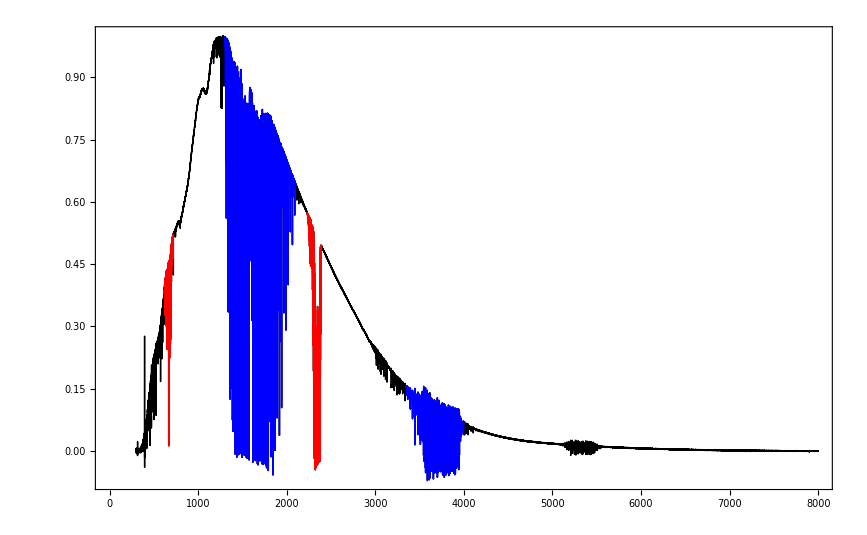

```mathematica
ListPlot[{Take[LuftNorm,{1,63875}],Take[LuftNorm,{46534,47859}],Take[LuftNorm,{60390,61220}],Take[LuftNorm,{33177,38574}],Take[LuftNorm,{48940,55578}]}, PlotStyle->{Black,Red,Red,Blue,Blue}]
```

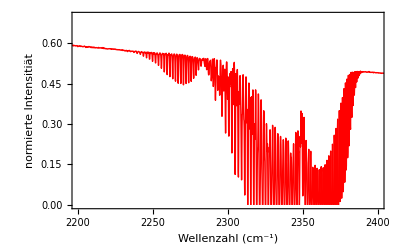

```mathematica
CO2a=ListPlot[LuftNorm,PlotRange->{{2200,2400},{0,0.7}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Red}]
```

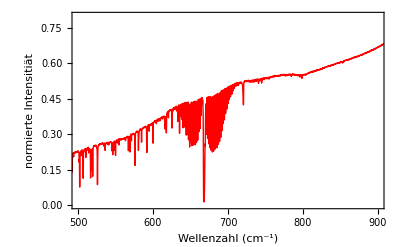

```mathematica
CO2b=ListPlot[LuftNorm,PlotRange->{{500,900},{0,0.8}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Red}]
```

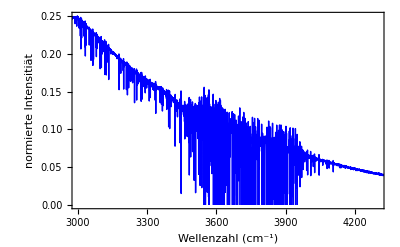

```mathematica
H2Oa=ListPlot[LuftNorm,PlotRange->{{3000,4300},{0,0.25}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Blue}]
```

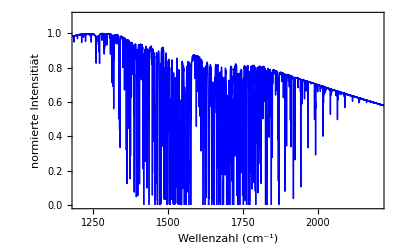

```mathematica
H2Ob=ListPlot[LuftNorm,PlotRange->{{1200,2200},{0,1.1}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Blue}]
```

## Signal-Rausch-Verhältnis

```mathematica
Rausch10=Import["D:\\Git\\F-Praktikum\\FKO\\Rohdaten\\01-N10.DPT","Table"];
Rausch50=Import["D:\\Git\\F-Praktikum\\FKO\\Rohdaten\\02-N50.DPT","Table"];
Rausch100=Import["D:\\Git\\F-Praktikum\\FKO\\Rohdaten\\03-N100.DPT","Table"];
```

0.999916

0.000555222

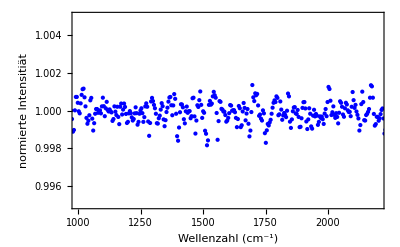

```mathematica
Mittelwert10=Mean[Rausch10[[1504;;1815]][[All,2]]]
Standardabweichung10=Sqrt[Mean[(Rausch10[[1504;;1815]][[All,2]]-Mean[Rausch10[[1504;;1815]][[All,2]]])^2]]
PlotRausch10=ListPlot[Rausch10,PlotRange->{{1000,2200},{0.995,1.005}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Blue},Joined->False]
```

1.00005

0.000275646

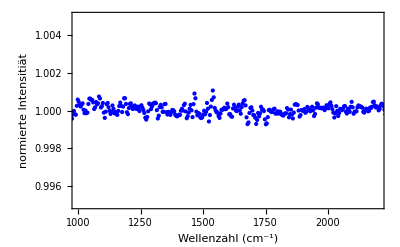

```mathematica
Mittelwert50=Mean[Rausch50[[1504;;1815]][[All,2]]]
Standardabweichung50=Sqrt[Mean[(Rausch50[[1504;;1815]][[All,2]]-Mean[Rausch50[[1504;;1815]][[All,2]]])^2]]
PlotRausch50=ListPlot[Rausch50,PlotRange->{{1000,2200},{0.995,1.005}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Blue},Joined->False]
```

1.00035

0.000171068

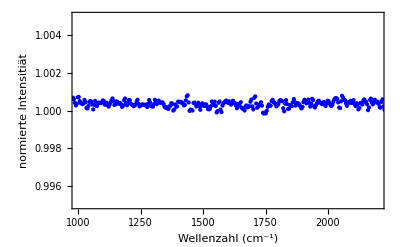

```mathematica
Mittelwert100=Mean[Rausch100[[1504;;1815]][[All,2]]]
Standardabweichung100=Sqrt[Mean[(Rausch100[[1504;;1815]][[All,2]]-Mean[Rausch100[[1504;;1815]][[All,2]]])^2]]
PlotRausch100=ListPlot[Rausch100,PlotRange->{{1000,2200},{0.995,1.005}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Blue},Joined->False]
```

```mathematica
nsquare={{Sqrt[10],Standardabweichung10},{Sqrt[50],Standardabweichung50},{Sqrt[100],Standardabweichung100}}
```

{{√10,0.000555222},{5 √2,0.000275646},{10,0.000171068}}

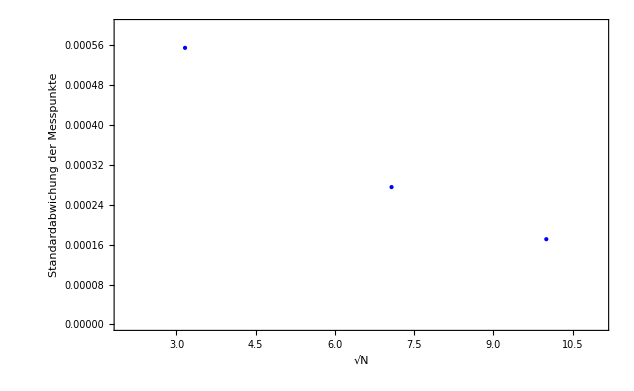

```mathematica
nsqurePlot=ListPlot[nsquare,PlotRange->{{2,11},{0,0.0006}},FrameLabel->{"√N","Standardabwichung der Messpunkte"},PlotStyle->{Blue},Joined->False]
```

## Bestimmung der Brechzahl

```mathematica
HrRGaAsundotiert=Import["D:\\Git\\F-Praktikum\\FKO\\Rohdaten\\04-GaAs-undotiert.DPT","Table"];
HrRGaAsdotiert=Import["D:\\Git\\F-Praktikum\\FKO\\Rohdaten\\05-GaAs-dotiert.DPT","Table"];
HrRSiundotiert=Import["D:\\Git\\F-Praktikum\\FKO\\Rohdaten\\06-Si-undotiert.DPT","Table"];
```

GaAs undotiert

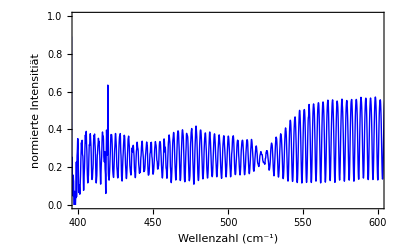
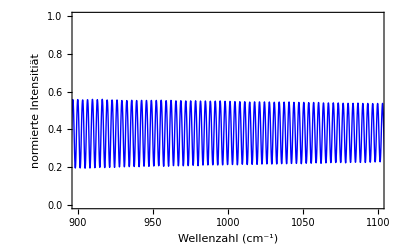
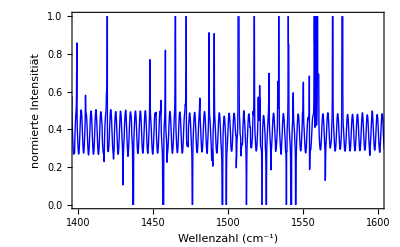
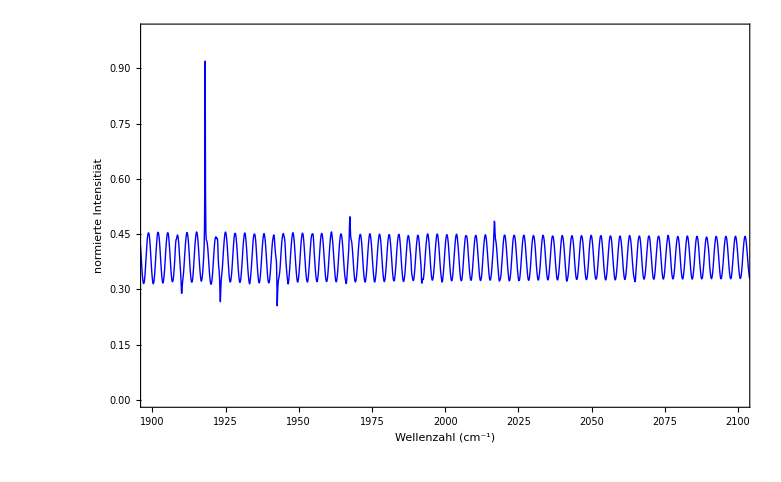
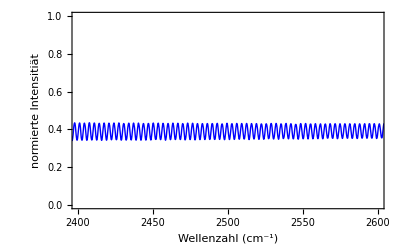
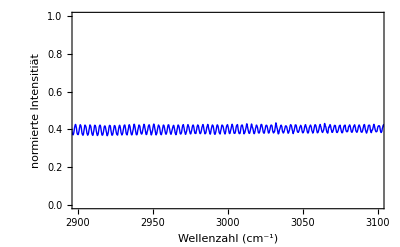
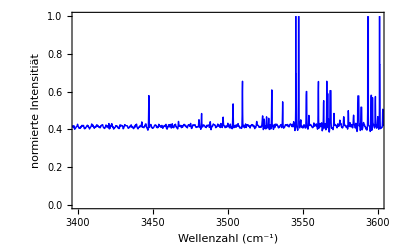
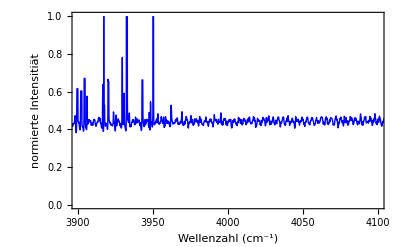

```mathematica
PlotHrRGaAsundotiert=Table[ListPlot[HrRGaAsundotiert,PlotRange->{ {i-100,i+100},{0,1}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Blue}],{i,500,5000,500}]
```

GaAs dotiert

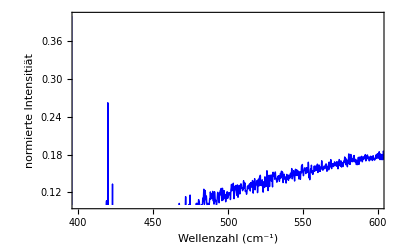
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotHrRGaAsdotiert=Table[ListPlot[HrRGaAsdotiert,PlotRange->{ {i-100,i+100},{0.1,0.4}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Blue}],{i,500,5000,500}]
```

```mathematica
PlotHrRSiundotiert=Table[ListPlot[HrRSiundotiert,PlotRange->{ {i-100,i+100},{0.1,0.7}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Blue}],{i,500,5000,500}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}